# Mikroskop

## Funktionen

### Includes

```mathematica
Needs["ErrorBarPlots`"]
```

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Gaussfunktion

```mathematica
Gauss[a_]:={Mean[a],StandardDeviation[a]/(√Length[a])}
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
Fdiv[a1_,da1_,b1_,db1_]:= Module[{f,fe,a,b,da,db},
f=a/b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1}]
```

```mathematica
Fmult[γ_,dγ_,δ_,dδ_]:= Module[{f,fe,a,b,da,db},
f=a*b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->γ,da->dγ,b-> δ,db->dδ}]
```

```mathematica
Ff[a1_,da1_,b1_,db1_,c1_,dc1_]:= Module[{f,fe,a,b,c,da,db,dc},
f=a*b/c;
fe = GError[f,{a,b,c},{da,db,dc}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1,c->c1,dc->dc1}]
```

## 1.1) Gesamtvergrößerung (Okular mit halbdurchlässigen Einblendspiegel)

```mathematica
t= {{140, 145, 150, 155, 160, 165, 170, 175, 180, 185}}*10^-3;
dt = 10^-3;
```

```mathematica
S1 = {{20, 20, 20, 20, 20, 20, 20, 20, 20, 20}}*10^-3;
ds1 = 2*10^-3;
S2 ={{0.439, 0.39, 0.37, 0.36, 0.35, 0.34, 0.33, 0.32, 0.31, 0.30}}*10^-3;
ds2 = 0.02*10^-3;
```

```mathematica
Vges = Table[Fdiv[S1[[1,x]],ds1,S2[[1,x]],ds2],{x,1,Length[S1[[1]]]}]
```

{{45.5581,6.63135},{51.2821,7.75805},{54.0541,8.32725},{55.5556,8.64198},{57.1429,8.97959},{58.8235,9.34256},{60.6061,9.7337},{62.5,10.1562},{64.5161,10.6139},{66.6667,11.1111}}

```mathematica
p1 = Table[{{t[[1,x]],Vges[[x,1]]},ErrorBar[dt,Vges[[x,2]]]},{x,1,Length[Vges]}]
```

{{{7/50,45.5581},ErrorBar[1/1000,6.63135]},{{29/200,51.2821},ErrorBar[1/1000,7.75805]},{{3/20,54.0541},ErrorBar[1/1000,8.32725]},{{31/200,55.5556},ErrorBar[1/1000,8.64198]},{{4/25,57.1429},ErrorBar[1/1000,8.97959]},{{33/200,58.8235},ErrorBar[1/1000,9.34256]},{{17/100,60.6061},ErrorBar[1/1000,9.7337]},{{7/40,62.5},ErrorBar[1/1000,10.1562]},{{9/50,64.5161},ErrorBar[1/1000,10.6139]},{{37/200,66.6667},ErrorBar[1/1000,11.1111]}}

```mathematica
pp= Table[{t[[1,x]],Vges[[x,1]]},{x,1,Length[Vges]}]
```

{{7/50,45.5581},{29/200,51.2821},{3/20,54.0541},{31/200,55.5556},{4/25,57.1429},{33/200,58.8235},{17/100,60.6061},{7/40,62.5},{9/50,64.5161},{37/200,66.6667}}

```mathematica
pf1=LinearModelFit[pp,x,x]
```

FittedModel[-9.62965+414.155 x]

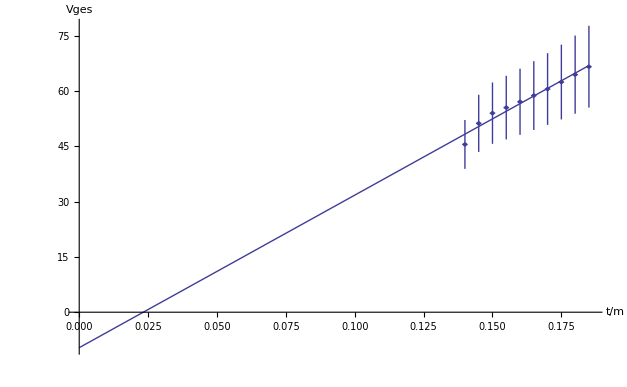

```mathematica
Show[
 ErrorListPlot[p1],
Plot[pf1[x],{x,0,Max[t]}],AxesLabel->{"t/m","Vges"},AxesOrigin->{0,0}]
```

```mathematica
pf1["ParameterTable"]
para1 = pf1["ParameterTableEntries"];
```

| Estimate | Standard Error | t Statistic | P-Value
1 | -9.62965 | 4.51679 | -2.13197 | 0.0655915
x | 414.155 | 27.6877 | 14.9581 | 3.93793×10^-7

```mathematica
xt = {para1[[1,1]],para1[[1,2]]}
```

{-9.62965,4.51679}

```mathematica
k={para1[[2,1]],para1[[2,2]]}
```

{414.155,27.6877}

```mathematica
l = Fdiv[Abs[xt[[1]]],xt[[2]],k[[1]],k[[2]]]
```

{0.0232513,0.0124605}

## 1.2) Objektivvergrößerung (Hilfsokular mit Okularmikrometer)

```mathematica
S3 = {{1, 1, 1, 1, 1, 1, 1, 1, 1, 1}}*0.5*10^-2;
ds3 = 5/100*10^-3*2;
S4 = {{0.53, 0.51, 0.5, 0.49, 0.47, 0.46, 0.44, 0.43, 0.42, 0.41}}*10^-3;
ds4 = 0.02*10^-3;
```

```mathematica
Vobj = Table[Fdiv[S3[[1,x]],ds3,S4[[1,x]],ds4],{x,1,Length[S3[[1]]]}]
```

{{9.43396,0.544678},{9.80392,0.580546},{10.,0.6},{10.2041,0.620575},{10.6383,0.665459},{10.8696,0.689981},{11.3636,0.743802},{11.6279,0.773391},{11.9048,0.804989},{12.1951,0.838786}}

## 2.) Okularvergrößerung

```mathematica
Vokt = Table[Fdiv[Vges[[x,1]],Vges[[x,2]],Vobj[[x,1]],Vobj[[x,2]]],{x,1,Length[Sok[[1]]]}]
```

{{4.82916,0.981738},{5.23077,1.10107},{5.40541,1.15705},{5.44444,1.17802},{5.37143,1.18008},{5.41176,1.20304},{5.33333,1.20566},{5.375,1.23094},{5.41935,1.25802},{5.46667,1.28711}}

```mathematica
Vok = Gauss[Vokt[[1;;Length[Vokt],1]]]
```

{5.32873,0.0593069}

```mathematica
dvok=1;
```

## 3) Objektivbrennweite

```mathematica
(*vgr = Table[Fmult[k[[1]],k[[2]],t[[1,x]],dt],{x,1,Length[t[[1]]]}];*)
```

```mathematica
fobjt = Table[Ff[t[[1,x]]-l[[1]],dt+l[[2]],Vok[[1]],dvok,Vges[[x,1]],Vges[[x,2]]],{x,1,Length[t[[1]]]}]
```

{{0.0136556,0.00612473},{0.0126509,0.00568664},{0.0124951,0.00559672},{0.012637,0.00562832},{0.0127522,0.00565224},{0.0128408,0.00566851},{0.0129027,0.00567711},{0.012938,0.00567805},{0.0129467,0.00567132},{0.0129287,0.00565693}}

```mathematica
fobj = Gauss[fobjt[[1;;Length[fobjt],1]]]
```

{0.0128748,0.0000994175}

## 4) Okularbrennweite

```mathematica
s0 = 25*10^-2;
ds0 = 0;
```

```mathematica
fok = Fdiv[s0,ds0,Vok[[1]],dvok]
```

{0.0469155,0.00880425}

## 5) Gesamtbrennweite

```mathematica
fges = Table[Ff[fobj[[1]],fobj[[2]],fok[[1]],fok[[2]],t[[1,x]]-l[[1]],dt+l[[2]]],{x,1,Length [t[[1]]]}];
fges 10^3
```

{{5.17373,1.60737},{4.96126,1.51786},{4.76554,1.4372},{4.58469,1.36418},{4.41705,1.2978},{4.26125,1.23723},{4.11606,1.18176},{3.98044,1.13079},{3.85347,1.08381},{3.73435,1.0404}}